# Random Graph Large

```mathematica
While@Not@ConnectedGraphQ[d=RandomGraph[{40,70},VertexLabels-> Placed[Automatic,Center],VertexSize->1]]
d
```

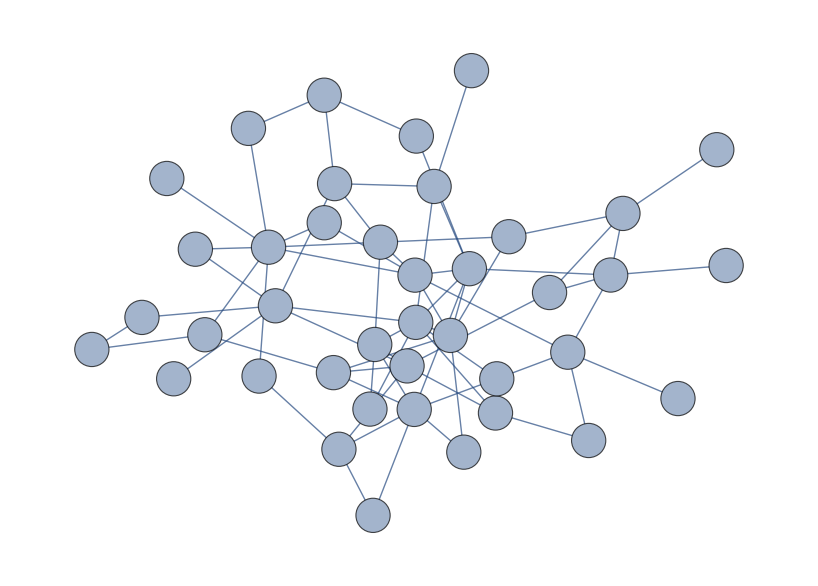

```mathematica
k=3;

vert=VertexList[d];
absvert=Length[vert];

edge=EdgeList[d];
edge=List @@@%;
absedge=Length[edge];

vertpoly={};
For[i=1,i≤absvert,i++,AppendTo[vertpoly,Indexed[x,i]^k-1]]

vars=Variables[vertpoly];

edgepoly={};
For[i=1,i≤absedge,i++,AppendTo[edgepoly,Part[PolynomialReduce[Indexed[x,Part[Part[edge,i],1]]^k-Indexed[x,Part[Part[edge,i],2]]^k,Indexed[x,Part[Part[edge,i],1]]-Indexed[x,Part[Part[edge,i],2]],{Indexed[x,Part[Part[edge,i],1]],Indexed[x,Part[Part[edge,i],2]]}],1]]];
edgepoly=Flatten[edgepoly];

graphpolyd=Join[vertpoly,edgepoly];

{test2,testgrob2}=AbsoluteTiming[GroebnerBasis[graphpolyd,vars,MonomialOrder->DegreeReverseLexicographic]]
```

{28.0948,{x31+x34+x38,201,-x13 x32 x35+x13 x33 x35+x32 x35^2-x33 x35^2+x13 x33 x37-x32 x33 x37+x13 x35 x37-x33 x35 x37-x35^2 x37+x13 x32 x33 x35^2 x37+x13 x33 x39-x32 x33 x39+x13 x35 x39-x33 x35 x39-x35^2 x39+x13 x32 x33 x35^2 x39+x13 x37 x39-x32 x37 x39-x35 x37 x39+x13 x32 x33 x35 x37 x39+x13 x32 x35^2 x37 x39-x32 x33 x35^2 x37 x39+x13 x32 x40-x32 x33 x40+x13 x35 x40-x32 x35 x40-x35^2 x40+x13 x32 x33 x35^2 x40-x32 x37 x40+x33 x37 x40+x13 x32 x35^2 x37 x40-x13 3 x40-1+x33 x39 x40+x13 x32 x35^2 x39 x40-x13 x33 x35^2 x39 x40+x37 x39 x40-x13 x32 x33 x37 x39 x40-x13 x33 x35 x37 x39 x40+x32 x33 x35 x37 x39 x40-x13 x35^2 x37 x39 x40+x33 x35^2 x37 x39 x40-x13 x40^2+x33 x40^2+x35 x40^2-x13 x32 x33 x35 x40^2-x13 x33 x35^2 x40^2+x32 x33 x35^2 x40^2+x37 x40^2-x13 x32 x33 x37 x40^2-x13 x32 x35 x37 x40^2+x32 x33 x35 x37 x40^2-x13 x35^2 x37 x40^2+x32 x35^2 x37 x40^2+x39 x40^2-x13 x32 x33 x39 x40^2-x13 x32 x35 x39 x40^2+x32 x33 x35 x39 x40^2-x13 x35^2 x39 x40^2+x32 x35^2 x39 x40^2-x13 x32 x37 x39 x40^2+x13 x33 x37 x39 x40^2+x32 x35 x37 x39 x40^2-x33 x35 x37 x39 x40^2}}
 |  |  |  |

```mathematica
Length[testgrob2]
```

203

```mathematica
sol=AbsoluteTiming[FindInstance[testgrob2==0,vars]]
```

{1134.84,{{x1→1/2 (-1-ⅈ √3),x2→1/2 (-1-ⅈ √3),x3→1/2 (-1-ⅈ √3),x4→1/2 (1+1/2 (-1-ⅈ √3))-1/2 √(2+ⅈ √3+1/4 (-1-ⅈ √3)^2),x5→1/2 (-1-ⅈ √3),x6→-1+1/2 (1+ⅈ √3),x7→1/2 (-1-ⅈ √3),x8→1/2 (1+1/2 (-1-ⅈ √3))-1/2 √(2+ⅈ √3+1/4 (-1-ⅈ √3)^2),x9→-1+1/2 (1+ⅈ √3),x10→1/2 (-1-ⅈ √3),x11→1/2 (-1-ⅈ √3),x12→1/4 (1+ⅈ √3)-1/2 √(4+2 (-1-ⅈ √3)+1/4 (-1-ⅈ √3)^2),x13→1/2 (-1-ⅈ √3),x14→1/2 (-1-ⅈ √3),x15→-1+1/2 (1+ⅈ √3),x16→-1+1/2 (1+ⅈ √3),x17→1/2 (-1-ⅈ √3),x18→1/2 (-1-ⅈ √3),x19→-1+1/2 (1+ⅈ √3),x20→1/2 (-1-ⅈ √3),x21→1,x22→1/2 (-1-ⅈ √3),x23→-1+1/2 (1+ⅈ √3),x24→1/2 (-1-ⅈ √3),x25→-1+1/2 (1+ⅈ √3),x26→-1+1/2 (1+ⅈ √3),x27→1,x28→1,x29→1,x30→-1+1/2 (1+ⅈ √3),x31→-1+1/2 (1+ⅈ √3),x32→1,x33→1/2 (-1-ⅈ √3),x34→1/2 (-1-ⅈ √3),x35→1,x36→1,x37→1,x38→1,x39→1/2 (-1-ⅈ √3),x40→1}}}

```mathematica
Expand[FullSimplify[Part[sol,2]]]
```

{{x1→-1/2-(ⅈ √3)/2,x2→-1/2-(ⅈ √3)/2,x3→-1/2-(ⅈ √3)/2,x4→-1/2-(ⅈ √3)/2,x5→-1/2-(ⅈ √3)/2,x6→-1/2+(ⅈ √3)/2,x7→-1/2-(ⅈ √3)/2,x8→-1/2-(ⅈ √3)/2,x9→-1/2+(ⅈ √3)/2,x10→-1/2-(ⅈ √3)/2,x11→-1/2-(ⅈ √3)/2,x12→-1/2+(ⅈ √3)/2,x13→-1/2-(ⅈ √3)/2,x14→-1/2-(ⅈ √3)/2,x15→-1/2+(ⅈ √3)/2,x16→-1/2+(ⅈ √3)/2,x17→-1/2-(ⅈ √3)/2,x18→-1/2-(ⅈ √3)/2,x19→-1/2+(ⅈ √3)/2,x20→-1/2-(ⅈ √3)/2,x21→1,x22→-1/2-(ⅈ √3)/2,x23→-1/2+(ⅈ √3)/2,x24→-1/2-(ⅈ √3)/2,x25→-1/2+(ⅈ √3)/2,x26→-1/2+(ⅈ √3)/2,x27→1,x28→1,x29→1,x30→-1/2+(ⅈ √3)/2,x31→-1/2+(ⅈ √3)/2,x32→1,x33→-1/2-(ⅈ √3)/2,x34→-1/2-(ⅈ √3)/2,x35→1,x36→1,x37→1,x38→1,x39→-1/2-(ⅈ √3)/2,x40→1}}